1.)

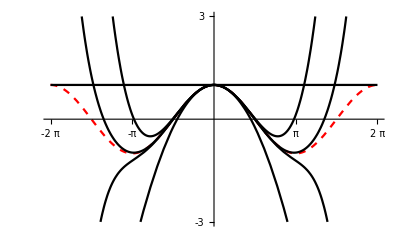

```mathematica
Plot[
{Cos[x],
Table[
Sum[(-1)^n x^(2n)/(2n)!,{n,0,k,1}],
{k,0,4,1}
]
},
{x,-2Pi,2Pi},
PlotStyle->{{Dashed,Red},Black},
PlotRange-> {{-2Pi,2Pi},{-3,3}},
Ticks->{{-2Pi,-Pi,Pi,2Pi},{-3,3}}
]
```

2.)

```mathematica
TeXForm[
TableForm[
Table[
{x,N[Sin[x Degree],4],N[Cos[x Degree],4],N[Tan[x Degree],4]},
{x,0,360,10}
],
TableHeadings->{None, {"angle","sine","cosine","tangent"}},
TableAlignments->Center
]
]
```

\begin{array}{cccc}
 \text{angle} & \text{sine} & \text{cosine} & \text{tangent} \\
 0 & 0 & 1.000 & 0 \\
 10 & 0.1736 & 0.9848 & 0.1763 \\
 20 & 0.3420 & 0.9397 & 0.3640 \\
 30 & 0.5000 & 0.8660 & 0.5774 \\
 40 & 0.6428 & 0.7660 & 0.8391 \\
 50 & 0.7660 & 0.6428 & 1.192 \\
 60 & 0.8660 & 0.5000 & 1.732 \\
 70 & 0.9397 & 0.3420 & 2.747 \\
 80 & 0.9848 & 0.1736 & 5.671 \\
 90 & 1.000 & 0 & \text{ComplexInfinity} \\
 100 & 0.9848 & -0.1736 & -5.671 \\
 110 & 0.9397 & -0.3420 & -2.747 \\
 120 & 0.8660 & -0.5000 & -1.732 \\
 130 & 0.7660 & -0.6428 & -1.192 \\
 140 & 0.6428 & -0.7660 & -0.8391 \\
 150 & 0.5000 & -0.8660 & -0.5774 \\
 160 & 0.3420 & -0.9397 & -0.3640 \\
 170 & 0.1736 & -0.9848 & -0.1763 \\
 180 & 0 & -1.000 & 0 \\
 190 & -0.1736 & -0.9848 & 0.1763 \\
 200 & -0.3420 & -0.9397 & 0.3640 \\
 210 & -0.5000 & -0.8660 & 0.5774 \\
 220 & -0.6428 & -0.7660 & 0.8391 \\
 230 & -0.7660 & -0.6428 & 1.192 \\
 240 & -0.8660 & -0.5000 & 1.732 \\
 250 & -0.9397 & -0.3420 & 2.747 \\
 260 & -0.9848 & -0.1736 & 5.671 \\
 270 & -1.000 & 0 & \text{ComplexInfinity} \\
 280 & -0.9848 & 0.1736 & -5.671 \\
 290 & -0.9397 & 0.3420 & -2.747 \\
 300 & -0.8660 & 0.5000 & -1.732 \\
 310 & -0.7660 & 0.6428 & -1.192 \\
 320 & -0.6428 & 0.7660 & -0.8391 \\
 330 & -0.5000 & 0.8660 & -0.5774 \\
 340 & -0.3420 & 0.9397 & -0.3640 \\
 350 & -0.1736 & 0.9848 & -0.1763 \\
 360 & 0 & 1.000 & 0 \\
\end{array}